```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
(*SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]*)
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];
```

```mathematica
LM=
Table[
MassValue=RandomReal[{1,9}]*10^0;
sigvalues =N[ RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==10^-9},sig,{n,1,65}]];
HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];
HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
HopfLine,
Joined->True,PlotRange->{{10^(-9),100},{10^(-9),100}},Frame->True
],
Graphics[Point[Log@MassPoint]],
Graphics[Line[{{Log@Growth/.M->MassValue,Log@(10^(-10))},{Log@Growth/.M->MassValue,Log@1000}}]]
}],
{10}];
```

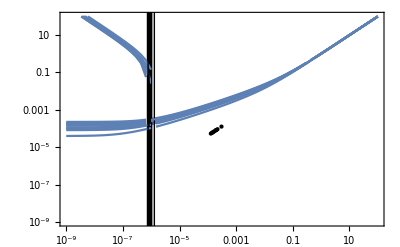

```mathematica
Show[{
LM
}]
```

```mathematica
Starvation/.M->MassValue - Growth/.M->MassValue
```

0.000093644

```mathematica
Growth/.M->MassValue
```

5.75344×10^-9

```mathematica
MassPoint
```

{1.93611×10^-7,1.23493×10^-8}

```mathematica
LM=Table[
MassValue=RandomReal[{1,5}]*10^1;
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,53}];
HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];
HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
HopfLine,
Joined->True,PlotRange->{{10^(-7),100},{0.001,100}},Frame->True
],
Graphics[Point[MassPoint]]
}],
{25}];
```

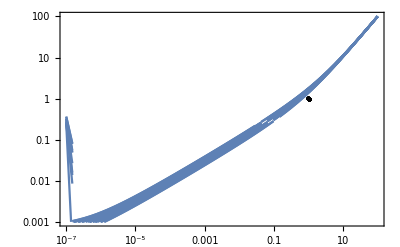

```mathematica
Show[LM]
```

```mathematica
MassPoint
```

{0.0000269665,1.05247×10^-6}

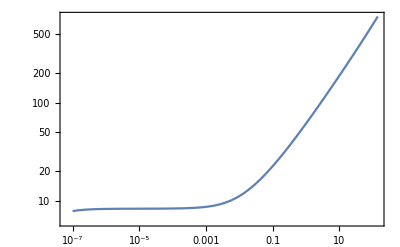

$Aborted

```mathematica
Show[{
ListLogLogPlot[
HopfLine,
Joined->True,PlotRange->{},Frame->True
],
Graphics[Point[MassPoint]]
}]
```